# <The Dot-To-Dot Poetry >

```mathematica
EntityRegister[EntityStore["Theoretical Physicist and Poet"-><|"Entities"-><|"V. Mazzeo"-><|"nationality"->"Italian"|>,"O. Sadinov"-><|"nationality"->"Italian"|>|>|>]];
```

```mathematica
EntityList["Theoretical Physicist and Poet"]
```

{V. Mazzeo,O. Sadinov}

If you look closely at a pointillist painting, you can see that it is made by individual dots of colour that are bits of paint like ‘atoms of matter’. On the other hand, if you read a poem, you can see that the words are arranged in separate lines, like an ‘electromagnetic spectrum’ which contains a ‘broad range of radiation’. In such a ‘literary spectrum’, human eye is able to see only the visible, i.e. the words.
People mentally process visual information that contains the fewest number of geometric shapes of Nature, according to Gestalt psychology, which states that “the whole is other than the sum of parts”.
Poetry and Mathematics are interrelated in many ways. Poets’ imagination has been fired by the elegance of numbers, from π  to the Fibonacci sequence. On the other hand, at a technical and practical level, Mathematics can be used to enhance our appreciation of poems.
Both poetry and mathematics struggle to express, by abstraction, the general behind the specific and to establish the essential and relevant by using arbitrary, convention-based symbolic systems.
Then, what is a poem, if not a combination of words which convey hidden messages through a symbolic meaning?

Goal of the Project

The goal of this project is to introduce the ‘dot-to-dot’ poetry by using the Wolfram Language. 
This project is a challenge, something new and difficult which has required great effort and determination, but also a great opportunity to “see the world in a grain of sand and a Heaven in a wild flower” (cit. W. Blake), the same flower appreciated by the physicist Richard Feynman in a famous interview: “I can appreciate the beauty of a flower. At the same time, I see much more about the flower (...), it’s not just beauty at this dimension, at one centimeter; there is also beauty at smaller dimensions, the inner structure (...)”.  The structures of poems and of other forms of writing reflect the tendency to see the text as a whole, not considering its smallest elements ( ‘quanta’), i.e. the letters.  
One of last exponents of visual poetry was Guillaume Apollinaire, who invented (or reinvented; the first poet to propose a pattern, or visual, poem was Theocritus, an ancient Greek poet in the 3rd century BC.) the figurative poem. Behind Apollinaire’s calligrams there were the force and inspiration of the Cubism movement. In Italy, F. T. Marinetti, the founder of the Futurist movement, proposed a concrete and sound poem as well. 

	-Graphics-				-Graphics-			-Graphics-

Marinetti built his poems as collages, cutting numbers and letters from newspapers and drawing some elements. Also in Mallarmé’s poem “Un Coup de Dés”,  we find words across the page for expressive purposes. Those visual characteristics constituted a poem’s innovation, with lines of text written from the upper left to the lower right through the book’s seam. 
Mallarmé, Apollinaire, Marinetti, all of them used white spaces to configure the reader’s visual experience. However, it is difficult to read a poem so plenty of white space between words, verses and stanzas, without linear and sequential patterns  of organization between units of meaning - be that sentence groups, phrases, words or even individual letters.   
A century later, we want to propose a new visual experience through literature, the ‘dot-to-dot’ poetry  (also known as ‘multi-layer poetry’), a new literary genre where science and art can complement each other based on both their differences and similarities: science is analytical; art is more intuitive. Most of mathematicians and physicists think of the representation of Nature in terms of symbols and images. Images. Undoubtedly, multilayer networks can allow us to better understand the structure of layers that represents a particular type of relationship between nodes in the natural world. 
In this project, we propose a technique to write dot-to-dot poems. The exploration/analysis of the text can be done by thinking and displaying letters/words as dots on a paper, or as nodes on a graph/layer. Like in the dot-to-dot game, nodes are dots and links are the lines that connect nodes to each other. If two or more nodes are connected via a link, it is assumed that the nodes have some sort of relationship with each other. By connecting nodes/dots/letters with links/lines, thus, it is possible to ‘visualize’ a poem and find hidden ‘objects’, such as quotes or poems.
In the figures below are shown two examples of dot-to-dot game: in Fig. 1, a sea horse (left), with dots to join, and a portrait of Salvador Dalì (right), with dots already linked to each other. In Fig. 2 it is shown an example of layers in the dot-to-dot poetry: the first layer (left), with the whole original text, and another layer (right), the last one, with only the letters that we need to join in the drawing. Between the first and the last layer there are other layers as many as the words/characters used in the drawing. For example: the word “In” can be decomposed on one layer (“In”) or in two layers (“I” on one layer, and “n” on another one). Let us suppose to arrange the letters of a word: in a permutation, the arrangement “In” and “Ni” are different; but, in a combination, the arrangements “In” and “Ni” are the same because the order is not important. Then, given an array of words, we can select them from the original text following a sequential order, even line by line, or consider, at the end of the selection, the anagrams made from our input letters or words.							
						                      		     -Graphics-							-Graphics-
										   														Fig.1

-Graphics-
										   													Fig.2

For this project, we use the Wolfram Language, a programming language that minimizes the complexity of code maintaining a unified and elegant structure and that allows us to represent text, code, graphics, documents,in terms of symbolic expressions.

#### Summary of the work

#### First of all, as a preliminary step, we need to import a text, such as a poem, and write, e.g., a quote that we would like to visualize in the text. Then, we clean up the text to have an idea about what we are trying to achieve. Cleaning text often means splitting it into tokens that would be useful for further text analysis. Words, numbers, punctuation marks, and others can be considered as tokens. After cleaning the text, we transform strings in lists of characters and count the characters to check of occurrences of common characters between the two strings (the text and the quote). Since we want to see “what everyone chooses not to see” (cit. Patch Adams), i.e. a 3D poem, we need to add a new layer to the previous one. This new layer contains the image that we want to overlay onto the text. In order to do this, we need to import the image, binarize it and delete its small components. By using MorphologicalPerimeter[] we can pick out the morphological perimeter of regions of foreground in our image (we can choose to use this image to be superimposed on the text or the original one). The Wolfram Predictive Interface streamlines the workflow, providing point-and-click image processing and graphics editing. By clicking on Coordinates Tool on the Image Assistant and Drawing Tools, we can select the number of points (equal to the number of characters/letters in the quote) on the image. This step could be also done by using the Ramer-Douglas-Peucker algorithm, which allows to reduce the number of points, and the Shi-Tomasi corner detector. However, in this article we will not use these algorithms. After selecting the dots on the text, we can plot, by using ListPlot[], the coordinates of the selected points, and convert the vector image to a raster image (Rasterize[]; we need to apply the Rasterize[] function also to the text). Finally, we compose the image, by joining the dots/letters. Let’s play, then, the dot-to-dot poetry and have fun!

### Code Explanation

#### Preprocessing : Text Import and Cleaning

#### We can also just copy and paste the text on the notebook:

```mathematica
text="Ancora una volta ti siederai al mio fianco,
come un crepuscolo che, sotto questo cielo,
fatica ad alzarsi. Durerà un secondo la mezzaluna.
La tua mano sfiorerà questa luce ossuta intrecciata a rami:
s’allungherà sull’ombra disfatta di erbe,
che s’attrizza ad ogni tuo gesto adagiato in me.
Senza la malinconia incompleta di noi,
impigliata alle labbra che incarnano il sogno,
ancora una volta ti siederai al mio fianco:
ed il tuo abbraccio sarà di me l’ala ferita
sotto cui il mio sguardo s’allontanerà dal volto.";
```

#### Then, we clean the text by replacing punctuation with white space

```mathematica
punctuation=Alternatives@@Characters[" ̀–,’.?:;'\"!-"];
```

#### and by writing lower case characters as well:

```mathematica
cleantext=StringReplace[ToLowerCase[text],punctuation->" "]
```

ancora una volta ti siederai al mio fianco 
come un crepuscolo che  sotto questo cielo 
fatica ad alzarsi  durerà un secondo la mezzaluna 
la tua mano sfiorerà questa luce ossuta intrecciata a rami 
s allungherà sull ombra disfatta di erbe 
che s attrizza ad ogni tuo gesto adagiato in me 
senza la malinconia incompleta di noi 
impigliata alle labbra che incarnano il sogno 
ancora una volta ti siederai al mio fianco 
ed il tuo abbraccio sarà di me l ala ferita
sotto cui il mio sguardo s allontanerà dal volto

#### Now, we transform the string in a list of characters

```mathematica
qtext=Characters[cleantext];
```

and count the number of times those characters appear in the string :

```mathematica
qtextCount=CharacterCounts[cleantext];
```

We can also plot the characters to see the cumulative frequency distribution of them in the text by using the ListPlot[] function:

```mathematica
ListPlot[%,Filling->Axis]
```

-Graphics-

#### The cumulative frequency table can help us analyze and understand the large amount of letters in the poem. It gives us a preliminary idea of the number of letters that we can consider for our quote. Therefore, we can write the quote that we want to visualize within the text; for example, we can use a quote by E. Montale, an Italian poet:

```mathematica
quote="In questo lago che è il tuo cuore. - E. Montale";
```

#### and count its number of characters by using StringLength[] (it will give us information about the number of dots what we need to use for ‘drawing’ the sentence):

```mathematica
charquote=Characters[quote];
quotelength=StringLength[StringReplace[quote, punctuation->""]]
```

34

#### By replacing the letters not included in the quote with white/blank spaces, we obtain the potential supporting structure for our drawing. We use the Complement[] function to find the elements in text that are not in the quote:

```mathematica
compl=Complement[Characters[text], charquote]
```

{,,:,
,à,A,b,d,D,f,L,m,p,S,v,z,’}

Then, we extract only the quote’s characters within the text and apply the Rasterize[] function, which returns a rasterized version of the displayed form of the text:

```mathematica
cleanquote=Rasterize[StringReplace[StringReplace[ToLowerCase[text], Except["\n", compl]->" "],punctuation->" "]]
```

-Graphics-

### Image Processing

In this subsection, we look at the image processing. 
The image that we want to reproduce in the text can be imported by using Import[] and resized by using the ImageResize[] function:

```mathematica
img=DeleteSmallComponents[Binarize[Image[Import@FileNameJoin[{NotebookDirectory[],"sw.jpg"}]]]];
resimage=ImageResize[img,{500,450}]
```

-Graphics-

Image::imgarray: The specified argument /Users/sadinov/Desktop/sw.jpg should be an array of rank 2 or 3 with machine-sized numbers.

Binarize::imginv: Expecting an image or graphics instead of Image[/Users/sadinov/Desktop/sw.jpg].

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of Binarize[Image[/Users/sadinov/Desktop/sw.jpg]].

ImageResize::imginv: Expecting an image or graphics instead of DeleteSmallComponents[Binarize[Image[/Users/sadinov/Desktop/sw.jpg]]].

ImageResize[DeleteSmallComponents[Binarize[Image[/Users/sadinov/Desktop/sw.jpg]]],{500,450}]

As you can see, we just converted the image  to a binary one, by using the Binarize[] function. This function replaces all pixels in the input image above a globally determined threshold with 1 and others with 0.
In order to reduce the number of dots in the image, we can use the DeleteSmallComponents[] function, which replaces small connected components in a binary image with background pixels, and the MorphologicalPerimeter[] function, which picks out the morphological perimeter of regions of foreground in the image:

```mathematica
MorphologicalPerimeter[img]
```

-Graphics-

By using ImageCompose[], we can combine more images by adding them into a new layer instead of overwriting the existing layers.
To use a custom control in Manipulate[], we can include the range used to generate the control object and see how it changes by scrolling the mouse on the slider. We can increase or decrease the size of the drawing, or move it up and down, to the left or to the right, and/or rotate it.  In this way, we can edit and ‘fit’ the image according to our text, and find the key points better matching the letters of the quote that we want to represent.

```mathematica
VPoetry=With[{grImp=Import@FileNameJoin[{NotebookDirectory[],"sw.jpg"}]},ColorReplace[grImp,First@DominantColors@grImp->Transparent]];
Manipulate[Module[{irGra},irGra=ImageResize[VPoetry,{s1,s2}];
ImageCompose[cleanquote,{irGra, 0.3},Scaled[{p1,p2}]]],{{p1,0.448},0.3,0.8},{{p2,0.495},0.3,0.8},{{s1,347.5},200,500},{{s2,298.},200,500}]
```

Once we have overlaid the two images and fit the drawing in the text, we can copy and paste the obtained image and start to investigate all sorts of structural relationships between the letters and the drawing. 

-Graphics-


In order to this, we should extract the positions of the letters within the text, representing them as points on a coordinate plane/graph. We get, then, the coordinates of these points:

```mathematica
coord={{327.3430259739265,195.63874092751985},{314.21715704683584,152.81519348237623},{261.2407090904911,177.98585191259764},{251.91639905883798,153.93894709412388},{285.2947262735961,111.78396192432388},{247.52807008131705,194.26961073599182},{309.71503023521393,198.12806854847986},{243.8723146608215,199.89193497704576},{271.8914751258843,219.74965702767537},{277.07638894211243,179.66792614790336},{264.2741326057467,196.29663465591628},{256.14825601447,196.38909539612337},{246.17316461905168,175.08756332533693},{300.95615319175033,72.47036642473375},{264.00386274975665,114.97741364378385},{238.929221242058,136.12602987499702},{271.0806655579145,94.1879718264521},{323.4098883328096,52.76911639599308},{225.2628126029875,27.964744744284303},{237.24714700675216,27.11126098852668},{176.51822160227476,30.06644849283782},{152.22238402170498,28.79333522383257},{58.44585635782552,52.31392505958905},{117.74519647140878,28.608413743418396},{239.57644642350763,10.286962453152682},{150.9101527472275,10.173164619051647},{51.38327827893039,28.569295737946163},{89.14637828889383,15.22294350728481},{4.185626585528482,74.47960943308016},{113.27151911831206,73.12470397081478},{20.252458287667565,113.93545222529639},{64.90032726074328,135.2476528430298},{174.18892218551932,92.6765943422979},{183.26074327276075,93.05354966775752},{150.75012454302293,115.7562175709129},{241.13405427776544,70.7171685431149},{207.89797435563358,92.20362209431545},{271.75278401557364,68.94263356760194},{228.62340489128357,134.57197820305493},{231.6390474949608,113.93900840761205},{235.81044935122665,178.84644803298664},{230.03520927059944,157.96454547544778},{239.80048590939404,198.93532193413398},{311.35443028273187,218.0284647868973},{319.61188561968777,150.85218084413344}};
```

To graph these points, we can use the ListPlot[] function, which plots a list of dots with specified x and y coordinates:

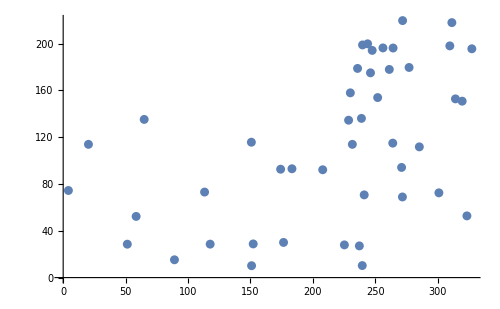

```mathematica
ListPlot[coord,ImageSize->{500,500},Axes->True]
```

To remove the axes from the plot, we need to set Axes to False:

```mathematica
Image[ListPlot[coord,ImageSize->{500,500},Axes->False]]
```

-Graphics-

The following plot shows the selected points. We can change the size of the dots, by using the size button.

```mathematica
img=Manipulate[Rasterize@ListPlot[coord,ImageSize->{500,500},Axes->False,PlotMarkers->{Automatic,Size}],{Size,{Tiny,Small,Medium,Large}},SaveDefinitions->True]
```

## Engage the reader!

This section is dedicated to the gentle reader. Many poets, but also literary critics even at TED talks, convey that people need poetry. In our opinion, they are wrong. We think that poetry needs people more than people need poetry. For this reason, we think it is important to actively involve and engage readers in literary activities, even conducting fun experiments like this one. 
We think, in fact, that readers, just like students at school, who are engaged in a task would read with more curiosity and enthusiasm poetry than readers who are not engaged. 
In order to increase the likelihood that readers will be engaged with poems, we need to turn poems into a game, i.e. the ‘dot-to-dot’ game,  to add a sense of ‘fun’ to reading them.
Then, as the last step, we connect the dots and find the hidden picture drawn by using the letters of the quote we chose. 
The animation below shows an image composition between a white page and the dots selected previously from our analysis. By using the Manipulate[] function,the reader can directly manipulate the cursor in the small window to draw.

```mathematica
Manipulate[ImageCompose[-Graphics-,Graphics[{{Orange,PointSize@.03,Point@pt},Line@AppendTo[curve,pt]},Axes->False,AxesLabel->{Style["x",Bold,16],Style["y",Bold,16]},PlotRange->{{-1,1},{-1,1}},ImageSize->Large]],{{pt,{0.0,0.0},Style["Move the point to connect the dots:",Bold,16]},{-1,-1},{1,1}},{{curve,{{0.0,0.0}}},None},TrackedSymbols->{pt}]
```

By using ImageCompose[], we can combine the text and the image into one.

```mathematica
image=ImageResize[Rasterize[ListLinePlot[coord, PlotMarkers->{Automatic,5}, Axes->False]],400]
```

-Graphics-

```mathematica
ImageCompose[Rasterize[text],{image, 0.3} , {145, 115}]
```

-Graphics-

```mathematica
CONCLUSION
```

As both P.L.Travers and J.Conrad said, “a writer is, after all, only half his book and his writes only half book. The other half is the reader and from the reader the writer learns”. What we really need is to “look beyond the fingers” (cit.Patch Adams), beyond that first layer which is in front of our eyes. The proof is left as an exercise to the reader.